# Lección 1- Bases y estados

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

```mathematica
<<Wolfram`QuantumFramework`
```

## Links importantes

WQF

https://www.wolfram.com/quantum-computation-framework/

Paclet Repository

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

Wolfram Community

https://community.wolfram.com/content/-/discussions-list/all+groups/Any+discussions/none/active/full/20/3/filter?curTag=quantum%20computing

https://community.wolfram.com/web/srodriguez

https://community.wolfram.com/web/brunot

Notebooks publicados

https://wolfr.am/QIS-Book

https://wolfr.am/QC-Book

https://www.wolframcloud.com/obj/srodriguez/Published/IntroductionToQuantumOptimization/TableOfContents.nb

Tech Notes

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/tutorial/SecondQuantization.html

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/tutorial/QuantumOptimization.html

Wolfram U Course

https://www.wolfram.com/wolfram-u/?s=quantum

https://www.wolfram.com/wolfram-u/courses/mathematics/wsg63-quantum-optimization/

https://www.wolfram.com/wolfram-u/courses/mathematics/wsg64-quantum-optics-second-quantization/

## Representación de bases: QuantumBasis

Base de dimension 2 (base computacional)

```mathematica
QuantumBasis[2]
```

QuantumBasis[…]

```mathematica
TraditionalForm[%]
```

<|0→{1,0},1→{0,1}|>

Cambia la dimensión

```mathematica
QuantumBasis[3]["Association"]
```

<|0→{1,0,0},1→{0,1,0},2→{0,0,1}|>

Dimensión de cada qudit y el número de qudits

```mathematica
TraditionalForm@QuantumBasis[2,3]["BasisStates"]
```

{000,001,010,011,100,101,110,111}

Pasa una asociación explicita para construir la base

```mathematica
qb =QuantumBasis[<|"up"->{1,1},"down"->{1,-ⅈ}|>];
qb["Association"]
```

<|up→{1,1},down→{1,-ⅈ}|>

Define base de polarización con argumentos de cadenas

```mathematica
qbPol = QuantumBasis[{"H","V"}]
```

<|H→{1,0},V→{0,1}|>

Usa bases nombradas

```mathematica
QuantumBasis["X"]["Association"]
```

<|𝓍_+→{1/(√2),1/(√2)},𝓍_−→{1/(√2),-1/(√2)}|>

```mathematica
QuantumBasis["Y"]["Association"]
```

<|𝓎_+→{1/(√2),ⅈ/(√2)},𝓎_−→{1/(√2),-ⅈ/(√2)}|>

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuditBasisNames
```

{Computational,PauliX,PauliY,PauliZ,Identity,I,X,Y,Z,JX,JY,JZ,J,JI,Bell,Fourier,Schwinger,Dirac,Ivanovic,Wigner,WignerMIC,Pauli,GellMann,GellMannMIC,Bloch,BlochSphere,GellMannBloch,GellMannBlochMIC,Wootters,Feynman,Tetrahedron,RandomMIC,RandomHaarMIC,RandomBlochMIC,QBismSIC,HesseSIC,HoggarSIC}

Base de bell para 2 qubits

```mathematica
QuantumBasis["Bell"]["Association"]
```

<|Φ^-→{1/(√2),0,0,-1/(√2)},Ψ^-→{0,1/(√2),-1/(√2),0},Ψ^+→{0,1/(√2),1/(√2),0},Φ^+→{1/(√2),0,0,1/(√2)}|>

Base con entrada y salida, base en el sentido de operadores

```mathematica
QuantumBasis[{"X"},{2}]["Association"]//Keys
```

{𝓍_+0,𝓍_+1,𝓍_−0,𝓍_−1}

Base con valores simbolicos

```mathematica
basis=QuantumBasis[<|"↑"->{x,y},"↓"->{z,w}|>]
```

<|↑→{x,y},↓→{z,w}|>

Los elementos de QuantumBasis no necesariamente  tienen que ser ortonormales al crearse la base

```mathematica
qb =QuantumBasis[<|"a"->{1,-3,0},"b"->{3,1,2},"c"->{2,-1,4}|>]
```

<|a→{1,-3,0},b→{3,1,2},c→{2,-1,4}|>

```mathematica
qb["OrthogonalElements"]
```

{{1/(√10),-3/(√10),0},{3/(√14),1/(√14),√(2/7)},{-3/(√35),-1/(√35),√(5/7)}}

```mathematica
OrthogonalMatrixQ[%]
```

True

Lista de propiedades

```mathematica
qb["Properties"]
```

{Association,BasisEffects,BasisMaps,BasisStates,ComputationalQ,ConjugateTranspose,Diagram,Dimension,Dimensions,Dual,ElementAssociation,ElementDimension,ElementDimensions,ElementNames,Elements,FinalParameters,FullInputQudits,FullOutputQudits,FullQudits,HasInputQ,InitialParameters,Input,InputBasis,InputDimension,InputDimensions,InputElementDimension,InputElementDimensions,InputElementNames,InputElements,InputMatrix,InputNameDimension,InputNameDimensions,InputQudits,InputRank,InputSize,InputTensor,Inverse,Label,LabelHead,Matrix,MatrixDimensions,MatrixElementDimensions,MatrixNameDimensions,MatrixRepresentation,NameDimensions,Names,NormalElementNames,OrthogonalElements,Output,OutputBasis,OutputDimension,OutputDimensions,OutputElementDimension,OutputElementDimensions,OutputElementNames,OutputElements,OutputMatrix,OutputNameDimension,OutputNameDimensions,OutputQudits,OutputRank,OutputSize,OutputTensor,ParameterArity,Parameters,ParameterSpec,Picture,Projectors,QuditBasis,Qudits,Rank,Size,Tensor,TensorDimensions,TensorRepresentation,Transpose,Type}

Base nombrada especificando número de qubits

```mathematica
QuantumBasis["Y",4]["Names"]
```

{𝓎_+𝓎_+𝓎_+𝓎_+,𝓎_+𝓎_+𝓎_+𝓎_−,𝓎_+𝓎_+𝓎_−𝓎_+,𝓎_+𝓎_+𝓎_−𝓎_−,𝓎_+𝓎_−𝓎_+𝓎_+,𝓎_+𝓎_−𝓎_+𝓎_−,𝓎_+𝓎_−𝓎_−𝓎_+,𝓎_+𝓎_−𝓎_−𝓎_−,𝓎_−𝓎_+𝓎_+𝓎_+,𝓎_−𝓎_+𝓎_+𝓎_−,𝓎_−𝓎_+𝓎_−𝓎_+,𝓎_−𝓎_+𝓎_−𝓎_−,𝓎_−𝓎_−𝓎_+𝓎_+,𝓎_−𝓎_−𝓎_+𝓎_−,𝓎_−𝓎_−𝓎_−𝓎_+,𝓎_−𝓎_−𝓎_−𝓎_−}

O con la dimensión para qudits

```mathematica
QuantumBasis["X"[3]]
```

<|𝓍_0→{1/(√3),1/(√3),1/(√3)},𝓍_1→{1/(√3),-(√3+ⅈ)/(√3 (√3-ⅈ)),(2 ⅈ)/(√3 (√3-ⅈ))},𝓍_2→{1/(√3),-(√3-ⅈ)/(√3 (√3+ⅈ)),-(2 ⅈ)/(√3 (√3+ⅈ))}|>

O ambas especificaciones

```mathematica
QuantumBasis["X"[3],2]["Names"]
```

{𝓍_0 𝓍_0,𝓍_0 𝓍_1,𝓍_0 𝓍_2,𝓍_1 𝓍_0,𝓍_1 𝓍_1,𝓍_1 𝓍_2,𝓍_2 𝓍_0,𝓍_2 𝓍_1,𝓍_2 𝓍_2}

Otro ejemplo (spin generalizado)

```mathematica
QuantumBasis["JY"[3]]
```

<|J_-3^y→{1/8,-1/4 ⅈ √(3/2),-(√15)/8,(ⅈ √5)/4,(√15)/8,-1/4 ⅈ √(3/2),-1/8},J_-2^y→{(√(3/2))/4,-ⅈ/2,-(√(5/2))/4,0,-(√(5/2))/4,ⅈ/2,(√(3/2))/4},J_-1^y→{(√15)/8,-1/4 ⅈ √(5/2),1/8,-(ⅈ √3)/4,-1/8,-1/4 ⅈ √(5/2),-(√15)/8},J_0^y→{(√5)/4,0,(√3)/4,0,(√3)/4,0,(√5)/4},J_1^y→{(√15)/8,1/4 ⅈ √(5/2),1/8,(ⅈ √3)/4,-1/8,1/4 ⅈ √(5/2),-(√15)/8},J_2^y→{(√(3/2))/4,ⅈ/2,-(√(5/2))/4,0,-(√(5/2))/4,-ⅈ/2,(√(3/2))/4},J_3^y→{1/8,1/4 ⅈ √(3/2),-(√15)/8,-(ⅈ √5)/4,(√15)/8,1/4 ⅈ √(3/2),-1/8}|>

Uso de producto tensorial (muchas veces no es necesario)

```mathematica
qbs = QuantumBasis/@{"X","Y"}
```

{QuantumBasis[…],QuantumBasis[…]}

```mathematica
QuantumTensorProduct@@qbs
```

<|𝓍_+𝓎_+→(1/2 | ⅈ/2
1/2 | ⅈ/2),𝓍_+𝓎_−→(1/2 | -ⅈ/2
1/2 | -ⅈ/2),𝓍_−𝓎_+→(1/2 | ⅈ/2
-1/2 | -ⅈ/2),𝓍_−𝓎_−→(1/2 | -ⅈ/2
-1/2 | ⅈ/2)|>

Definición de una base paramétrica 1/(√2)(|0⟩ ± ⅇ^(ⅈ θ) |1⟩ )

```mathematica
eb = QuantumBasis[<|"θ_+"->{1,Exp[I θ]}/√2,"θ_-"->{1,-Exp[I θ]}/√2|>,"Parameters"->θ]
```

<|θ_+→{1/(√2),ⅇ^(ⅈ θ)/(√2)},θ_-→{1/(√2),-ⅇ^(ⅈ θ)/(√2)}|>

```mathematica
eb["Parameters"]
```

{θ}

```mathematica
eb[0]
```

<|θ_+→{1/(√2),1/(√2)},θ_-→{1/(√2),-1/(√2)}|>

```mathematica
eb[π/2]==QuantumBasis["Y"]
```

True

## Representación de estados: QuantumState

Definición de un estado simbólico

```mathematica
ψ =QuantumState[{α,β},2]//TraditionalForm
```

α0+β1

```mathematica
QuantumState[{α,β}]["Amplitudes"]
```

<|0→α,1→β|>

Por defecto se considera una base computacional

```mathematica
ψ=QuantumState[{3,2,ⅈ 5,1}]
```

300+201+5 ⅈ10+11

Normaliza el estado

```mathematica
ψ["Normalize"]
```

√(3/13)00+2/(√39)01+(5 ⅈ)/(√39)10+1/(√39)11

Especifica la base de qudit

```mathematica
ψ=QuantumState[{3,2,ⅈ 5,1},4]["Normalize"]
```

√(3/13)0+2/(√39)1+(5 ⅈ)/(√39)2+1/(√39)3

Extrae el vector de estado( como SparseArray o lista)

```mathematica
QuantumState[{1,2ⅈ+1,3}]["StateVector"]
```

SparseArray[…]

```mathematica
QuantumState[{1,2ⅈ+1,3}]["AmplitudeList"]
```

{1,1+2 ⅈ,3}

Extrae las probabilidades

```mathematica
QuantumState[{a,b}]["Probability"]
```

<|0→Abs[a]^2/(Abs[a]^2+Abs[b]^2),1→Abs[b]^2/(Abs[a]^2+Abs[b]^2)|>

```mathematica
QuantumState[{a,b,c,0}]["ProbabilityList"]
```

{Abs[a]^2/(Abs[a]^2+Abs[b]^2+Abs[c]^2),Abs[b]^2/(Abs[a]^2+Abs[b]^2+Abs[c]^2),Abs[c]^2/(Abs[a]^2+Abs[b]^2+Abs[c]^2),0}

```mathematica
QuantumState[{a,b,0,0}]["Probability"]
```

<|00→Abs[a]^2/(Abs[a]^2+Abs[b]^2),01→Abs[b]^2/(Abs[a]^2+Abs[b]^2)|>

```mathematica
QuantumState[{a,b,0,0}]["Probabilities"]
```

<|00→Abs[a]^2/(Abs[a]^2+Abs[b]^2),01→Abs[b]^2/(Abs[a]^2+Abs[b]^2),10→0,11→0|>

Simplifica probabilidades

```mathematica
QuantumState[{a ⅇ^(ⅈ ϕ),b}]["ProbabilityList"]
```

{(ⅇ^(-2 Im[ϕ]) Abs[a]^2)/(ⅇ^(-2 Im[ϕ]) Abs[a]^2+Abs[b]^2),Abs[b]^2/(ⅇ^(-2 Im[ϕ]) Abs[a]^2+Abs[b]^2)}

```mathematica
ComplexExpand[%]
```

{a^2/(a^2+b^2),b^2/(a^2+b^2)}

Usa la notación daga de mecánica cuántica

```mathematica
ψ =QuantumState["R"]
```

1/(√2)0+ⅈ/(√2)1

```mathematica
ψ["Dagger"]
```

1/(√2)0-ⅈ/(√2)1

```mathematica
SuperDagger[ψ]
```

1/(√2)0-ⅈ/(√2)1

Producto interno

```mathematica
(SuperDagger[ψ]@ψ)
```

QuantumState[…]

```mathematica
(SuperDagger[ψ]@ψ)["Scalar"]
```

1

Construir estados con strings

```mathematica
QuantumState["111"]
```

111

Crea una superposición

```mathematica
1/(√2)(QuantumState["010"]+QuantumState["111"])
```

1/(√2)010+1/(√2)111

Usa un estado nombrado

```mathematica
ψ=QuantumState["PhiMinus"]
```

1/(√2)00-1/(√2)11

Lista de estados nombrados

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuantumStateNames
```

{0,Zero,Up,1,One,Down,Plus,Minus,Left,Right,PsiPlus,PsiMinus,PhiPlus,PhiMinus,BasisState,Register,UniformSuperposition,UniformMixture,RandomPure,RandomMixed,GHZ,Bell,Dicke,W,Werner,Graph,BlochVector}

Uso de parámetros en estados

```mathematica
linearPol =QuantumState[{Cos[θ],Sin[θ]},qbPol,"Parameters"->θ]
```

cos(θ)H+sin(θ)V

```mathematica
linearPol[0]
```

H

```mathematica
linearPol[π/4]
```

1/(√2)H+1/(√2)V

Estado simbolico en la base de Pauli X

```mathematica
QuantumState[{a,b},"X"]
```

a𝓍_++b𝓍_−

Realizar un cambio de base

```mathematica
QuantumState[{a,b}]
```

a0+b1

```mathematica
QuantumState[%,"X"]
```

(a/(√2)+b/(√2))𝓍_++(a/(√2)-b/(√2))𝓍_−

Estados aleatorios puros

```mathematica
QuantumState["RandomPure"]
```

(-0.851371+0.33021 ⅈ)0+(0.0629975+0.40269 ⅈ)1

```mathematica
QuantumState["RandomPure",{2,2}]
```

(0.5521-0.266429 ⅈ)00+(-0.153327+0.32767 ⅈ)01+(-0.0886725-0.0650758 ⅈ)10+(0.69187+0.0504244 ⅈ)11

```mathematica
QuantumState["RandomPure",4]
```

(0.174377+0.00674895 ⅈ)0+(0.403297-0.126291 ⅈ)1+(-0.699929+0.342238 ⅈ)2+(0.367537+0.220994 ⅈ)3

Estado GHZ

```mathematica
QuantumState["GHZ"]
```

1/(√2)000+1/(√2)111

Estado Grafo

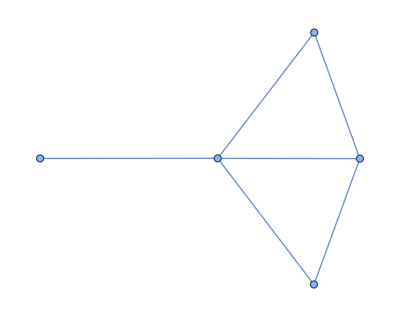

```mathematica
g =RandomGraph[{5,6}]
```

```mathematica
QuantumState["Graph"[g]]
```

QuantumState[…]

Superposiciones uniformes

```mathematica
QuantumState["UniformSuperposition"[3]]
```

1/(2 √2)000+1/(2 √2)001+1/(2 √2)010+1/(2 √2)011+1/(2 √2)100+1/(2 √2)101+1/(2 √2)110+1/(2 √2)111

```mathematica
QuantumState["UniformSuperposition",10]
```

1/(√10)0+1/(√10)1+1/(√10)2+1/(√10)3+1/(√10)4+1/(√10)5+1/(√10)6+1/(√10)7+1/(√10)8+1/(√10)9

Define un estado mixto , dando como argumento una matriz

```mathematica
ψ = QuantumState[{{0.6,0.2},{-0.3,0.4}}]
```

QuantumState[…]

```mathematica
ψ["DensityMatrix"]//MatrixForm
```

(0.6 | 0.2
-0.3 | 0.4)

Estados aleatorios mixtos

```mathematica
ψ = QuantumState["RandomMixed"]
```

(0.649459+0. ⅈ)00+(-0.0441756-0.218318 ⅈ)01+(-0.0441756+0.218318 ⅈ)10+(0.350541+0. ⅈ)11

Propiedades de QuantumState

```mathematica
QuantumState["Properties"]
```

{Amplitude,AmplitudeList,AmplitudePlot,Amplitudes,AmplitudesList,Association,Basis,BasisEffects,BasisMaps,BasisStates,Bend,BendDual,Bipartition,BlochCartesianCoordinates,BlochPlot,BlochSphericalCoordinates,CircuitDiagram,Computational,ComputationalQ,Conjugate,ConjugateTranspose,Decompose,DecomposeWithAmplitudes,DecomposeWithProbabilities,DensityMatrix,Diagram,Dimension,Dimensions,Disentangle,Double,Dual,Eigenstates,Eigenvalues,Eigenvectors,ElementAssociation,ElementDimension,ElementDimensions,ElementNames,Elements,Entropy,FinalParameters,Formula,FullInputQudits,FullOutputQudits,FullQudits,FullSimplify,HasInputQ,InitialParameters,Input,InputBasis,InputDimension,InputDimensions,InputElementDimension,InputElementDimensions,InputElementNames,InputElements,InputMatrix,InputNameDimension,InputNameDimensions,InputQudits,InputRank,InputSize,InputTensor,Inverse,Kind,Label,LabelHead,LogicalEntropy,Matrix,MatrixDimensions,MatrixElementDimensions,MatrixNameDimensions,MatrixQ,MatrixRepresentation,MatrixState,Mixed,MixedStateQ,NameDimensions,Names,Norm,NormalElementNames,NormalizedAmplitudes,NormalizedDensityMatrix,NormalizedOperator,NormalizedProjector,NormalizedQ,NormalizedState,NormalizedStateVector,NumberQ,NumericQ,Operator,OrthogonalElements,Output,OutputBasis,OutputDimension,OutputDimensions,OutputElementDimension,OutputElementDimensions,OutputElementNames,OutputElements,OutputMatrix,OutputNameDimension,OutputNameDimensions,OutputQudits,OutputRank,OutputSize,OutputTensor,ParameterArity,Parameters,ParameterSpec,PauliTree,Physical,PhysicalQ,Picture,PieChart,PrimeBasis,Probabilities,ProbabilitiesList,Probability,ProbabilityList,ProbabilityPlot,Projector,Projectors,Pure,PureStateQ,Purify,Purity,QuditBasis,Qudits,Rank,Reverse,ReverseInput,ReverseOutput,Scalar,SchmidtBasis,SchmidtDecompose,SectorChart,Simplify,Size,SpectralBasis,Split,SplitDual,State,StateMatrix,StateTensor,StateType,StateVector,Table,Tensor,TensorDimensions,TensorRepresentation,TensorReverseInput,TensorReverseOutput,Trace,TraceNorm,Transpose,Type,Unbend,UniformBasis,UnknownQ,Unpurify,VectorQ,VectorState,VonNeumannEntropy,Weights}

```mathematica
QuantumState["RandomMixed"]["Purity"]
```

0.588426

Propiedades gráficas (probabilidades, amplitudes, esfera de Bloch)

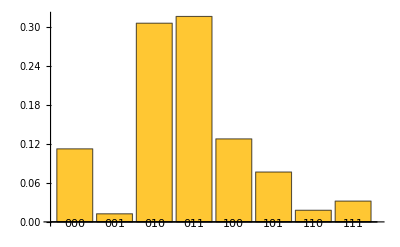

```mathematica
QuantumState["RandomPure"[3]]["ProbabilityPlot"]
```

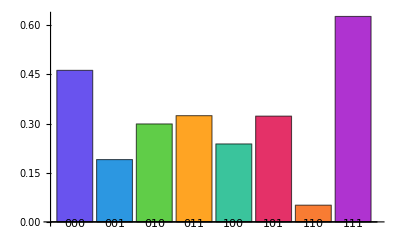

```mathematica
QuantumState["RandomPure"[3]]["AmplitudePlot",ChartLegends->Automatic]
```

```mathematica
QuantumState["RandomMixed"]["BlochPlot"]
```

-Graphics3D-

## Ejercicios

Dada la base ortonormal {𝓊=(1
0), 𝒹=(0
1)}, normaliza los siguientes estados:

ψ=3𝓊+(1+5i)𝒹

ϕ=i/2 𝓊-3/4 𝒹

Del anterior problema:

Calcula ϕψ y ψϕ

Plotea en la esfera de Bloch ψ=√(3/4)𝓊-ⅈ √(1/4)𝒹

Un estado cuántico también puede escribirse como ψ=Cos[θ/2]𝓊+ⅇ^ⅈϕ Sin[θ/2]𝒹, donde los ángulos pueden interpretarse geométricamente en la esfera de Bloch. Muestra en la esfera de Bloch todas los estados posibles para cada θ y ϕ.

Del anterior problema calcula los eigenvectors y muestralos en la esfera de Bloch. Utiliza un rango de valores para θ y ϕ tal que el vector se encuentra dentro de la esfera de Bloch.

Muestra que dos vectores ortonormales están ubicados en puntos antipodales de la esfera de Bloch.

Sea ρ_1 la matriz densidad del estado ψ^-, y ρ_2 la matriz densidad del estado mixto uniforme. Calcula λ ρ_1 + (1-λ) ρ_2 y halla sus autovalores y autoestados

Calcula la matriz densidad de un estado que tiene un vector de Bloch {x,y,z} (utiliza un named state)

Define la base de polarización de dos fotones en t.08erminos de polarización diagonal y antidiagonal, las etiquetas deben estar correctas y usar las relaciones de como se expresan los estados |D⟩ y |A⟩ en términos de |H⟩ y |V⟩. Prueba que el estado de Bell Φ^+ tiene la misma forma expresado en la base de H y V que en la base de A y D

Genera un sistema cuántico compuesto por tres subsistemas C^2⊗C^3⊗C^5

Encuentra forma alternativas de generar el mismo estado que  QuantumTensorProduct@@QuantumBasis/@{"X","Y"}

Se observa:

```mathematica
QuantumState[{a,b,c},2]
```

¿Qué dimensión mínima tiene un sistema de dimensión 2?

¿Qué está ocurriendo internamente si pasas 3 amplitudes?

¿Está el framework truncando?

¿Está reinterpretando la dimensión?

12. Ejecuta

```mathematica
QuantumState[{1,2,3,5,7},2]["AmplitudesList"]
```

¿Cuál es la dimensión total del espacio si se pasa 2?

¿Por qué aparecen 8 entradas?

¿Qué regla está usando el framework para completar?

¿Qué tipo de sistema representa 2 como argumento?

Generaliza: si pasas dimensión d y k amplitudes, ¿cuántos ceros agrega?